# Illustratio of Video tracking

## Step 0 - Load the program

```mathematica
Quit[];
```

```mathematica
<<VideoTracking`
$HistoryLength = 2; (*prevent memory overload*)
Options[FFmpeg]={
"Colors"->1 (*number of color channels*),"ColorCommand"->"gray" (*indicator for "-pix_fmt" parameter:gray/rgb24*)
};

Begin["VideoTracking`Private`"]
SelectParticles[img_]:=Intersection[
FilterSize[img,OptionValue[VideoTracking,FilterArea]],FilterCircularity[img,OptionValue[VideoTracking,FilterCircularity]]
(*,FilterHoles[img]*)
]
End[]
```

VideoTracking`Private`

VideoTracking`Private`

## Step 1 - Select the video file

```mathematica
SelectVideo[ "/Users/kmisiunas/Google Drive/PhD/Software/video-tracking/practice_videos/video_3.avi"]
```

video_3.avi has 878 frames and is 1024x768

## Step 2 - Select region of intrest

```mathematica
SelectROI[({{377, 435}, {647, 435}, {647, 85}, {377, 85}})]
```

(377 | 435
647 | 435
647 | 85
377 | 85)

## Step 3 - Compute the background image

```mathematica
LoadAllFrames[]
```

```mathematica
bg = UpdateBackgroung[1, NumberOfFrames[]]
```

-Graphics-

```mathematica
meanBG = MeanBackground[Range@300]
```

-Graphics-

```mathematica
ImageDifference[bg, meanBG]//ImageAdjust
```

-Graphics-

## Step 4 - configure tracing algorithm

```mathematica
Options[VideoTracking];

SetOptions[VideoTracking, 
 FilterCircularity -> {0.5, 1.2},
 FilterArea -> {40, 220},
 UpdateBackgroung -> False,
 Threshold -> Automatic
]
```

{Threshold→Automatic,FilterArea→{40,220},FilterCircularity→{0.5,1.2},AnalysisBlockSize→4000,UpdateBackgroung→False,BackgroundAlgorithm→SmartMeanBackground,MinThreshold→0.05}

```mathematica
(*avi filter: DV video*)
SetOptions[VideoTracking, 
 FilterCircularity -> {0.5, 1.2},
 FilterArea -> {16, 60},
 UpdateBackgroung -> False,
 Threshold -> Automatic
]
```

{Threshold→Automatic,FilterArea→{16,60},FilterCircularity→{0.5,1.2},AnalysisBlockSize→4000,UpdateBackgroung→False,BackgroundAlgorithm→SmartMeanBackground,MinThreshold→0.05}

## Step 5 - Inspect per frame basis (run many times!)

(153.434 | 139.63
229.918 | 101.817)

-Graphics-

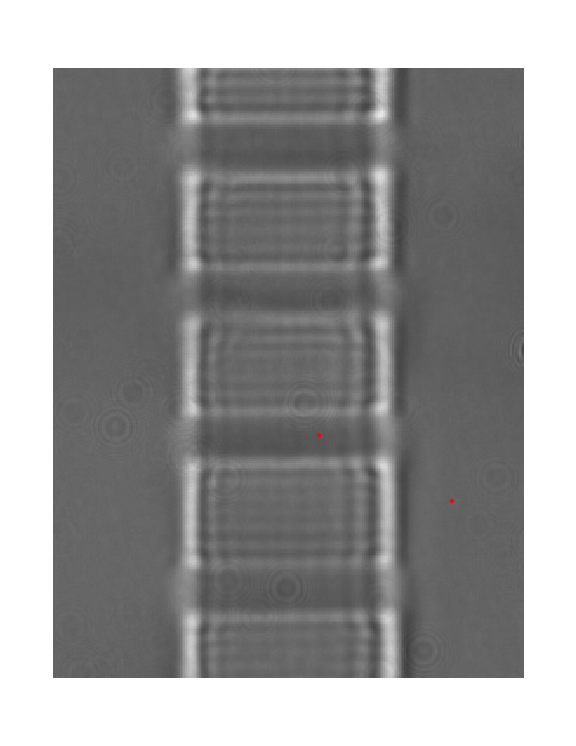

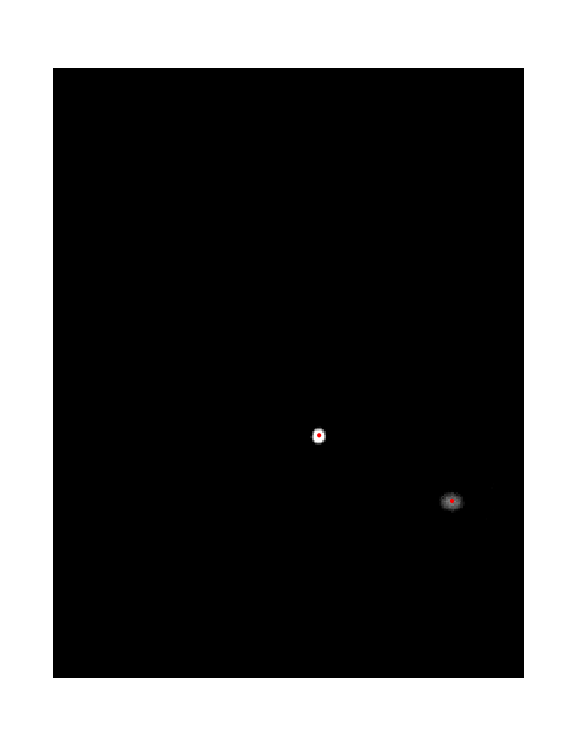

-Graphics-

Area→{1→66.,2→87.625}

Circularity→{1→1.04636,2→0.906797}

```mathematica
frame =132;

ShowTrackOverlayed[img_,list_]:=Show[img,Graphics@Flatten@{Red,Point[#]&/@list},ImageSize->Large]

curPos = AnalyseFrame[frame]
ShowTrackOverlayed[ GetFrame[frame] , curPos]
ShowTrackOverlayed[ CurrentBackground[], curPos]
ShowTrackOverlayed[ ImageAdjust[SubstractBG@GetFrame[frame], {0.5,1.6}] , curPos] 
ShowTrackOverlayed[ FrameBinarize@SubstractBG@GetFrame[frame] , curPos]

"Area"-> ComponentMeasurements[ FrameBinarize@SubstractBG@GetFrame[frame] ,"Area"]

"Circularity"-> ComponentMeasurements[ FrameBinarize@SubstractBG@GetFrame[frame] ,"Circularity"]
```

```mathematica
GetFrame[frame]
```

-Graphics-

## Step 6 - Define plot function

```mathematica
roiSize = { ROICurrent[]⟦3,1⟧-ROICurrent[]⟦1,1⟧,-ROICurrent[]⟦3,2⟧+ROICurrent[]⟦1,2⟧};

offset = {-0.5,0};

DrawCross[pos_, size_:10.0]:= If[
pos⟦1⟧>size && pos⟦1⟧<(roiSize⟦1⟧-size) && pos⟦2⟧>size  &&pos⟦2⟧<(roiSize⟦2⟧-size)
,
{
Line[{pos - {size,0} + offset, pos + {size,0}+ offset}],
Line[{pos - {0,size}+ offset, pos + {0,size}+ offset}]
}
,
{}]

ShowCustomOverlayed[img_,list_]:=Show[img,Graphics@Flatten@{Red,DrawCross[#]&/@list},
ImageSize->Large]

ShowCustomOverlayed[ GetFrame[frame] , AnalyseFrame[frame]]
```

-Graphics-

## Step 7 - generate all the frames

```mathematica
images = Table[

ShowCustomOverlayed[ GetFrame[frame] , AnalyseFrame[frame]]

,
{frame, frame, NumberOfFrames[]}
];
```

```mathematica
{Slider[ Dynamic@f, {1,NumberOfFrames[],1}], Dynamic@f}
```

{,}

```mathematica
Dynamic@images⟦f⟧
```

```mathematica
images⟦2⟧
```

-Graphics-

```mathematica
Export[ "/Users/kmisiunas/Google Drive/PhD/Presentation/2014/Conference in Sicily, July /images/ip_animation.gif", images⟦;;300⟧]
```

$Aborted

```mathematica
images⟦700⟧
```

-Graphics-